# Machine Learning the Optimal Cryptocurrency Portfolio from Blockchain Activity

Shivain Vij

Philip Maymin

Cryptocurrencies are notoriously unpredictable with traditional financial approaches. This project will utilize historical blockchain activity to construct a machine learning algorithm that would be able to optimize intraday cryptocurrency portfolio allocations. The results would be compared to traditional financial approaches to identify the success rate of the machine learned algorithm.

What’s left:
- Organize Notebook so it is easier to read (Remove lines that are unnecessary, 
- Create functions to filter/sort/organize raw data so it is ready to be put into ML
- Implement ML to predict optimized portfolio from blockchain activity across several cryptocurrencies
- Test against current financial approaches

```mathematica
btc = FinancialData["BTC/USD",{2016, 07, 18}];
eth = FinancialData["ETH/USD", {2008, 1, 1}];
ImageDifference[DateListPlot[eth], DateListPlot[btc]]
```

The above graph shows that Bitcoin and Ethereum’s prices fluctuate in similar patterns

```mathematica
btcstddev = Drop[Flatten[Import["bitcoinity_data.xlsx"]],2]; (*Useless*)
btcvolatility= ArrayReshape[btcstddev, {1640, 2}];(*Useless*)
DateListPlot[btcvolatility, PlotRange->All]; (*Useless*)
```

```mathematica
ethstddev = Drop[Flatten[Import["ETH.csv"]], 2];(*Useless*)
ethvolatility = ArrayReshape[ethstddev, {513, 2}]; (*Useless*)
```

```mathematica
stddev = Drop[Flatten[Import["bitcoinity_data.xlsx"]],2]; (*Useless*)
```

```mathematica
portfolio={"BTC","ETH"};
data =FinancialData[#, {{2010},{2020}}]&/@portfolio
returns=Differences@*Log/@data
MatrixForm[stddev, [[2, 2]]];  (*Useless*)
```

```mathematica
TimeSeriesResample[{dataBTC, dataETH},"Intersection"]
```

{{{Day: Mon 18 Jul 2016,676.88},{Day: Tue 19 Jul 2016,674.57},{Day: Wed 20 Jul 2016,673.215},{Day: Thu 21 Jul 2016,666.02},{Day: Fri 22 Jul 2016,664.255},{Day: Sat 23 Jul 2016,648.865},{Day: Sun 24 Jul 2016,655.05},980,{Day: Mon 1 Jul 2019,10760.4},{Day: Tue 2 Jul 2019,10579.6},{Day: Wed 3 Jul 2019,10807.},{Day: Thu 4 Jul 2019,11968.5},{Day: Fri 5 Jul 2019,11136.},{Day: Sat 6 Jul 2019,11004.2},{Day: Sun 7 Jul 2019,11196.4}},{1}}
 |  |  |  |

{{{Day: Mon 18 Jul 2016,676.88},{Day: Tue 19 Jul 2016,674.57},{Day: Wed 20 Jul 2016,673.215},{Day: Thu 21 Jul 2016,666.02},{Day: Fri 22 Jul 2016,664.255},{Day: Sat 23 Jul 2016,648.865},{Day: Sun 24 Jul 2016,655.05},980,{Day: Mon 1 Jul 2019,10760.4},{Day: Tue 2 Jul 2019,10579.6},{Day: Wed 3 Jul 2019,10807.},{Day: Thu 4 Jul 2019,11968.5},{Day: Fri 5 Jul 2019,11136.},{Day: Sat 6 Jul 2019,11004.2},{Day: Sun 7 Jul 2019,11196.4}},{1}}
 |  |  |  |

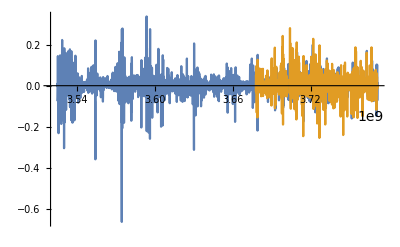

```mathematica
ListLinePlot[returns, PlotRange -> All]
```

```mathematica
StandardDeviation[returns[[1]]] (*Standard Deviation/volatility of BTC*)
StandardDeviation[returns[[2]](*Standard Deviation/volatility of ETH*)
```

```mathematica
Correlation[returns[[1]]["Values"], returns[[2]]["Values"]];
```

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

```mathematica
portfolio={"BTC","ETH"};
dataBTC =FinancialData["BTC", {{2016},{2020}}];
dataETH = FinancialData["ETH", {{2010},{2020}}];
returns=Differences@*Log/@data;
```

```mathematica
dataBTC[]
dataETH[]
TimeSeriesThread
```

```mathematica
TimeSeriesThread[Total,{dataBTC, dataETH}]
```

InterpolatingFunction::dmval: Input value {3660595200} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3660681600} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3660768000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

TimeSeries[…]

```mathematica
Mean[returns[[1]]]
```

0.00261812

Mean[{TimeSeries[…],TimeSeries[…]}⟦3⟧]

0.00254955

0.00261812

```mathematica
optimize[Mean[returns[[1]]], Mean[returns[[2]]], btcvolatility, ethvolatility, correlation];
```

```mathematica
optimize[btcreturn_, ethreturn_, btcvolatility_, ethvolatility_, correlation_] := NMaximize[(weight*btcreturn+(1-weight)*ethreturn)/Sqrt[btcvolatility^2 + ethvolatility^2 + (2*correlation*btcvolatility*ethvolatility)], weight]
```

```mathematica
optimize[0.0026181158079658356]
```

SCRAP CODE BELOW

```mathematica
ToExpression/@(StringReplace[#,","->""]&/@BTCData[[2;;, 2]])// Normal;
BTCData[[2;;, 1]]//Normal;
Riffle[ToExpression/@(StringReplace[#,","->""]&/@BTCData[[2;;, 2]])// Normal, BTCData[[2;;, 1]]//Normal]
```

```mathematica
BlockchainTransactionData[BlockchainBlockData[1000000]["TransactionList"]]//Dataset
```

Dataset[<>]

```mathematica
stddev = Drop[Flatten[Import["bitcoinity_data.xlsx"]],2];
portfolio={"BTC","ETH"};
data =FinancialData[#, {{2010},{2020}}]&/@portfolio
returns=Differences@*Log/@data
MatrixForm[stddev, [[2, 2]]]

ListLinePlot[returns, PlotRange -> All]
Optimization


Select[Table[(BlockchainTransactionData[BlockchainBlockData[x]["TransactionList"]]//Dataset)[[1,8]], {x, 1}], # ≠ Quantity[50., "Bitcoins"]&]
DateListPlot[({Interpreter["DateTime"][First[#]],Last[#]})&/@Table[ArrayReshape[StringSplit[btcJuly,{",","\t","\n"}],{1827,12}][[x]][[{1,12}]], {x, 2, 10}]]
ArrayReshape[StringSplit[stddev,{" ","\t","\n"}],{1641,2}][[x]][[{1,2}]]
```

{TimeSeries[…],TimeSeries[…]}

{TimeSeries[…],TimeSeries[…]}

```mathematica
data=FinancialData[#,"Price",{{2016},{2017},"Month"}][[All,2]]&/@Portfolio;
```

Part::partd: Part specification … is longer than depth of object.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Log[TemporalData[TimeSeries,{{{380.828,430.92,413.715,456.42,526.24,633.33,653.72,575.555,605.08,693.125,730.975,959.13,963.88}},{{{«13»}}},1,{Discrete,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic}},True,12.]⟦All,2⟧]].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Log[TemporalData[TimeSeries,{{{12.44,11.2,13.1879,10.9491,8.58691,8.14838,8.11922}},{{{«7»}}},1,{Discrete,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic}},True,12.]⟦All,2⟧]].

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Log[{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]⟦All,2⟧,TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]⟦All,2⟧}⟦3⟧]].

General::stop: Further output of Differences::listrp will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

Part::partw: Part 4 of … does not exist.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
stddev = Drop[Flatten[Import["bitcoinity_data.xlsx"]],2]; (*Useless*)
portfolio={"BTC","ETH"};
data =FinancialData[#, {{2010},{2020}}]&/@portfolio
returns=Differences@*Log/@data
MatrixForm[stddev, [[2, 2]]]
```